```mathematica
carryOverMoment[k_]:= (2k)/(3 + 4 k)
```

```mathematica
Table[ {k, carryOverMoment[k]//N}, {k, {0, 1, 1.5, 2, 3, 4, 10^9.}}] // MatrixForm
```

(0 | 0.
1 | 0.285714
1.5 | 0.333333
2 | 0.363636
3 | 0.4
4 | 0.421053
1.×10^9 | 0.5)

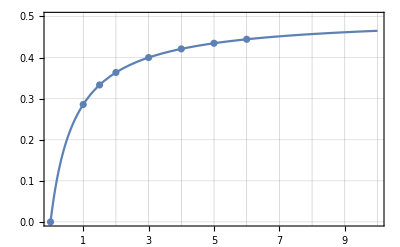

```mathematica
Show[
Plot[carryOverMoment[k], {k, 0, 10}, PlotRange -> {0, 0.5}, Frame -> True,
GridLines->{Range[1,10], Automatic}, FrameTicks->{Range[1,10], Automatic}
],
ListPlot[Table[Tooltip[ {k, carryOverMoment[k]//N},carryOverMoment[k]//N] , {k, {0, 1, 1.5, 2, 3, 4, 5, 6,10^9.}}]]
]
```